```mathematica
Clear["Global`*"]
Clear[ndf,pdf,cdf]
ndf[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
(*cdf=Function[{θ,α},Evaluate[Integrate[2*π*ndf[θ,α]*Cos[θ]*Sin[θ],θ]]]*)
cdf[θ_,α_]:=(1-Cos[θ]^2)/(1+Cos[θ]^2*(α^2-1))
pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
pdfCos[cosθ_,α_]:=α^2/(π*(cosθ^2*(α^2-1)+1)^2)*cosθ
```

Error in Mip Interpolation

We’re interested in the error we make when we linearly interpolate the mips of the cube map encoding various values of roughness for each mip.
We know that there’s an almost linear relationship between the squared roughness β=α^2 and the squared cosine of the half lobe angle μ^2

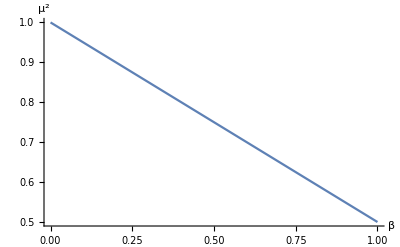

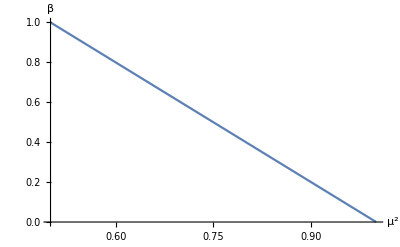

```mathematica
Clear[fSqRoughness2SqCos,fSqCos2SqRoughness]
(*fSqRoughness2SqCos[x_]:= (5.238881411332154-1.5797129260127443 x^2)/(5.238881411332154+1.5265349072841383 x+0.6923074066106989 x^2)
fSqCos2SqRoughness[x_]:= (160.3332299994536-131.2107114069501 x-29.133792073234147 x^2)/(41.83893846650725+168.13611151303041 x-153.7500633778045 x^2)*)

(* Super simple version *)
fSqCos2SqRoughness[μ2_]:=2*(1-μ2)
fSqRoughness2SqCos[β_]:=1-β/2

(*fSqCos2SqRoughness=Function[y,x=2*(1-y); 0.01+1.4827516714288516*x-1.0381908729571114*x^2+0.5454431449123816*x^3];
fSqRoughness2SqCos=Function[x,1-1/2*((1.3675780565697848 x-0.46349896024802306 x^2)/(2.259534233469395-2.4219546454815024 x+1.0664995083338693 x^2))];*)



Plot[fSqRoughness2SqCos[β],{β,0,1},PlotRange->Full,AxesLabel->{"β","μ^2"}]
Plot[fSqCos2SqRoughness[μ2],{μ2,1/2,1},PlotRange->Full,AxesLabel->{"μ^2","β"}]
```

But the correspondance between mip and squared cosine is logarithmic:

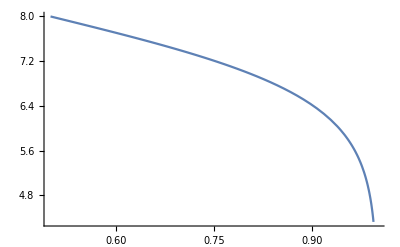

```mathematica
mipMax=8;
sqMu2Mip[μ2_]:= mipMax + 1/2*Log2[1/μ2-1]
mip2SqMu[mip_]:=1/(1+2^(2(mip-mipMax)))
Plot[sqMu2Mip[μ2],{μ2,1/2,1}]
```

Here’s the plot of the requested mip level that would actually be needed for a linear progression of β=α^2:

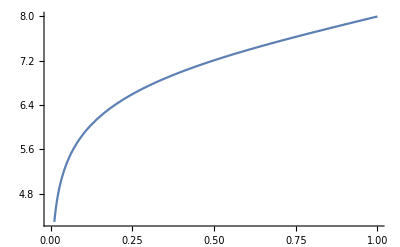

```mathematica
Plot[sqMu2Mip[fSqRoughness2SqCos[β]],{β,0,1}]
```

Here’s a plot of the squared roughness values encoded in each mip:

{0.999985,0.999939,0.999756,0.999024,0.996109,0.984615,0.941176,0.8,0.5}

{0.00552423,0.0110482,0.0220944,0.0441726,0.0882162,0.175412,0.342997,0.632456,1.}

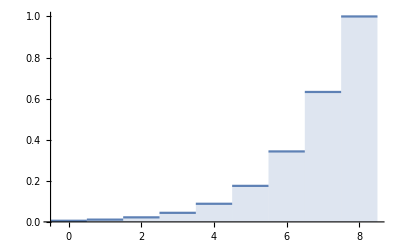

```mathematica
Table[N[mip2SqMu[m]],{m,0,mipMax}]
Table[N[√fSqCos2SqRoughness[mip2SqMu[m]]],{m,0,mipMax}]
DiscretePlot[√fSqCos2SqRoughness[mip2SqMu[m]],{m,0,mipMax},ExtentSize->Full]
```

First we notice the roughness are extremely poorly distributed and we should change our mapping
  => The first 4 mips all contain the same squared roughness since the squared cosine of the half angle stays mostly the same and almost = 1
  => And it’s already the SQUARE of the cosine, the cosine itself would be even more poorly distributed as it would even more stick to 1!

Second, the linear interpolation of 2 mips is certainly not equivalent to the expected roughness!